```mathematica
ClearAll["Global`*"];

(* ==========================================*)
(*1. 参数设置 (平滑且稳定的参数)*)
(* ==========================================*)
Dcoef=0.5;   (*扩散系数*)
r=0.8;       (*反应/传染率*)
K=1.0;       (*容量上限*)
gamma=0.1;   (*康复/衰减率*)
L=15;        (*正方形空间区域[-L,L]*)
tMax=20;     (*模拟总时间*)

(* ==========================================*)
(*2. 初始条件 (三个爆发源，模拟波前融合)*)
(* ==========================================*)
initCond=u[x,y,0]==0.4*Exp[-((x-5)^2+(y-5)^2)/3]+0.3*Exp[-((x+6)^2+(y+2)^2)/4]+0.5*Exp[-((x-2)^2+(y+6)^2)/3];

(* ==========================================*)
(*3. 显式边界条件 (核心修复：三变量偏导数必须写 3 个参数)*)
(* ==========================================*)
bc={Derivative[1,0,0][u][-L,y,t]==0,Derivative[1,0,0][u][L,y,t]==0,Derivative[0,1,0][u][x,-L,t]==0,Derivative[0,1,0][u][x,L,t]==0};

(* ==========================================*)
(*4. 偏微分方程主体*)
(* ==========================================*)
pde=D[u[x,y,t],t]==Dcoef*Laplacian[u[x,y,t],{x,y}]+r*u[x,y,t]*(1-u[x,y,t]/K)-gamma*u[x,y,t];

(* ==========================================*)
(*5. PDE 高精度数值求解*)
(* ==========================================*)
Print["正在进行高精度数值求解，请稍候..."];
sol=NDSolveValue[{pde,initCond,bc},u,{t,0,tMax},{x,-L,L},{y,-L,L},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->50,"MaxPoints"->100}}];

(* ==========================================*)
(*6. 渲染精美 3D 动画帧序列*)
(*注意：这里使用 PlotLabel，避免产生 PlotTitle 错误*)
(* ==========================================*)
Print["正在渲染 3D 图像序列..."];
frames=Table[Plot3D[sol[x,y,t],{x,-L,L},{y,-L,L},PlotRange->{0,K},ColorFunction->"TemperatureMap",PlotStyle->Directive[Opacity[0.9],Specularity[White,50]],Mesh->None,AxesLabel->{"X","Y","Proportion"},BoxRatios->{1,1,0.4},PlotLabel->Style[Row[{"Spatiotemporal Spread at t = ",NumberForm[t,{3,1}]}],14,Bold,FontFamily->"Helvetica"],ImageSize->700,ViewPoint->{2,-2.5,1.5},SphericalRegion->True],{t,0,tMax,0.5}];

Print["生成完毕！你可以直接预览动图："];
ListAnimate[frames,AnimationRate->10]

(*如果你想导出这个动图放到 PPT 里，取消注释下面这行代码运行即可*)
(*Print["动图已保存至当前 Mathematica 文件所在目录。"];*)
```

正在进行高精度数值求解，请稍候...

正在渲染 3D 图像序列...

生成完毕！你可以直接预览动图：

NotebookDirectory::nosv: 没有保存笔记本 obj.

SetDirectory::badfile: 指定参数 $Failed 应为有效字符串或文件.

```mathematica
SetDirectory[NotebookDirectory[]];
Export["COVID_Spatial_Wave.gif",frames,"DisplayDurations"->0.1];
```

正在进行全域空间积分，这可能需要十几秒钟的时间，请稍候...

积分完成！正在生成演化曲线：

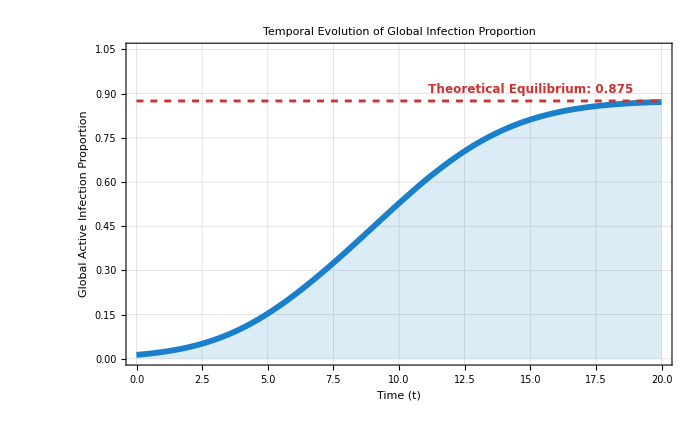

```mathematica
(* ==========================================*)(*7. 空间积分：计算宏观总感染率随时间的演化*)(* ==========================================*)Print["正在进行全域空间积分，这可能需要十几秒钟的时间，请稍候..."];

(*定义数值积分函数，对全域求积分后除以总面积 (2L)*(2L)，得到平均感染比例*)
Clear[TotalInfection];
TotalInfection[t_?NumericQ]:=NIntegrate[sol[x,y,t],{x,-L,L},{y,-L,L},AccuracyGoal->4,PrecisionGoal->4]/(4*L^2);

(*离散化时间点并并行计算 (每 0.5 秒提取一个点)*)
timeSteps=Range[0,tMax,0.5];
integralData=Table[{t,TotalInfection[t]},{t,timeSteps}];

(*计算系统最终的理论稳态上限 (Equilibrium State)*)
(*当 ru(1-u/K)-gamma*u==0 时，解得非零稳态 u* =K(1-gamma/r)*)
theoreticalMax=K*(1-gamma/r);

(* ==========================================*)
(*8. 绘制顶级期刊质感的 2D 演化曲线*)
(* ==========================================*)
Print["积分完成！正在生成演化曲线："];
infectionPlot=ListLinePlot[integralData,InterpolationOrder->3,(*使用 3 阶样条插值，让曲线像丝绸一样平滑*)PlotStyle->Directive[Thickness[0.006],RGBColor[0.1,0.5,0.8]],(*高级深海蓝*)Filling->Axis,FillingStyle->Directive[RGBColor[0.1,0.5,0.8],Opacity[0.15]],(*底部填充半透明颜色*)Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{Style["Time (t)",14,Bold],Style["Global Active Infection Proportion",14,Bold]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],PlotLabel->Style["Temporal Evolution of Global Infection Proportion",16,Bold,FontFamily->"Helvetica"],(*使用 Epilog 注入理论水平虚线和文本标注*)Epilog->{Directive[RGBColor[0.8,0.2,0.2],Dashed,Thickness[0.003]],Line[{{0,theoreticalMax},{tMax,theoreticalMax}}],Text[Style["Theoretical Equilibrium: "<>ToString[theoreticalMax],RGBColor[0.8,0.2,0.2],12,Bold],{tMax*0.75,theoreticalMax+0.04}]},PlotRange->{{0,tMax},{0,1.05}},(*留出顶部呼吸空间*)ImageSize->700]

(*同样，如果你需要将其导出为高清图片，可以取消下方注释*)
(*Export["C:\\Users\\user\\Desktop\\Global_Infection_Evolution.png",infectionPlot,ImageResolution->300];*)
```